# A billiard ball as a point reflected elastically inside a region

Define a region
Discretizes the region into a MeshRegion. 
Then given its boundary edge indices, find all boundary edges
Given a point on one of the edges, define a direction and a ray (green line)
Find the first edge that the ray intersect
Given the intersection point, find the reflection by considering the edge at the intersection point
Repeat this process

## Ball confined in a region

Define a region:

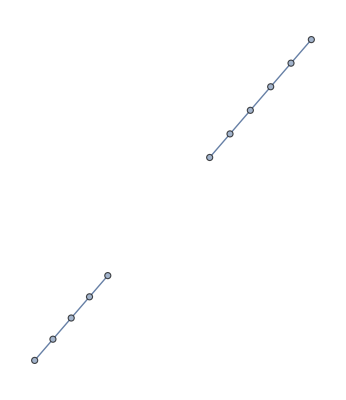

```mathematica
DiscretizeRegion[RegionIntersection[reg,ray1]]//MeshConnectivityGraph
```

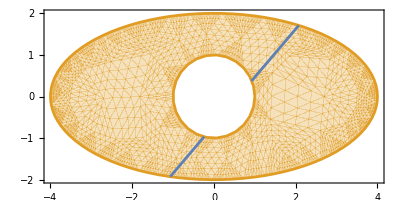

```mathematica
RegionPlot[{RegionIntersection[reg,ray1],reg},AspectRatio->1/2]
```

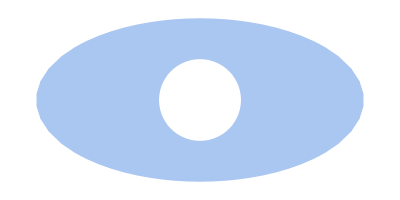

```mathematica
reg= RegionDifference[Disk[{0,0},{4,2}],Disk[]]
(*RegionUnion[-Graphics-,-Graphics-]*)
(*RegionDifference[Rectangle[{-2,-2},{2,2}],Disk[{0,0},1]]*)
(*StadiumShape[]*)
```

Find all of its boundary edges:

```mathematica
edges=boundaryEdges[reg,MeshCellMeasure->{"Length"->.001}];
```

From boundary edges, pick one randomly and one point within that:

```mathematica
edge1=RandomChoice[edges];
p1=Mean@@edge1;
```

From the initial point, pick a ray in a given direction
Make sure the ray does not go outside of the region

```mathematica
Manipulate[Graphics[{{Opacity[.3],DiscretizeRegion@reg},{Red,PointSize[Medium],Point[p1]},{Green,Dynamic[ray1=HalfLine[p1,pnt2-p1]]}}],{{pnt2,Mean@@RandomChoice[edges]},Locator}]
```

Given initial edge, point, and ray, find all 200 reflections within the region:

```mathematica
final=NestList[reflect[#,edges]&,{p1,edge1,ray1},100];//AbsoluteTiming
```

{2.96934,Null}

Find all rays reflected within the region:

```mathematica
lines=Line/@Partition[final[[All,1]],2,1];
```

Visualize them:

```mathematica
Manipulate[Graphics[{{edges,Opacity[.2],LightBlue,DiscretizeRegion@reg},{Red,Opacity[.2],lines[[;;s]]},{Blue,lines[[s]]}}],{s,1,Length[lines],1}]
```

### NDSolve

```mathematica
ray1
```

HalfLine[{17.6715,-6.80175},{-30.2271,9.19953}]

```mathematica
ray1[[2]]
```

{-30.2271,9.19953}

```mathematica
V[{x_Real, y_Real}]:= With[{d=SignedRegionDistance[reg,{x,y}]},
                                                           If[d<0,0, 10^6 d^2]]
```

```mathematica
F[{x_Real, y_Real}]:= With[{d=SignedRegionDistance[reg,{x,y}], eps=10^-6},
                                                           -{V[{x+eps/2, y}]-V[{x-eps/2, y}],V[{x, y+eps/2}]-V[{x, y-eps/2}]}/eps ]
```

```mathematica
nds=NDSolve[{X''[t]==F[X[t]], X[0]==p1, X'[0]==ray1[[2]]}, X, {t, 0, 200},Method->"BDF", MaxStepSize->10^-2]
```

NDSolve::ndsz: At t == 98.0121, step size is effectively zero; singularity or stiff system suspected.

{{X→InterpolatingFunction[{{0., 98.0121}}, <>]}}

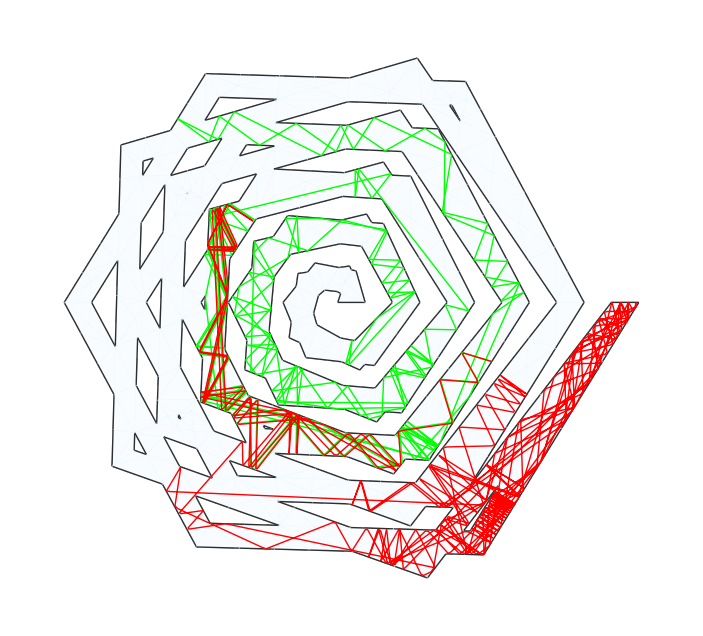

```mathematica
Show[{Graphics[{{edges,Opacity[.2],LightBlue,DiscretizeRegion@reg},{Green,lines[[;;200]]}}],
         ParametricPlot[Evaluate[X[t]/. nds[[1]]],{t,0,50},PlotStyle->Directive[Red,Thin]]}]
```

## Initializations

Given a region, first discretizes a region reg into a MeshRegion. Then given its boundary edge indices, find all boundary edges, which will be a collection of lines

```mathematica
ClearAll[boundaryEdges];
boundaryEdges[reg_,opts:OptionsPattern[]]:=
Module[{dg,boundaryedgeindices},
dg=DiscretizeRegion[reg,FilterRules[{opts}, Options[DiscretizeRegion]]];
boundaryedgeindices=Flatten@Position[Length/@dg["ConnectivityMatrix"[1,2]]["AdjacencyLists"],1];MeshPrimitives[dg,{1,boundaryedgeindices}]]
```

Given an initial point, edge and ray, find the reflection inside a region with its given boundary edges. The result will be the next point on edges, its corresponding edge element and ray reflected from that point

```mathematica
ClearAll[reflect];
reflect[{p1_,edge1_,ray1_},boundaryedges_]:=Module[
{boundaryLines,edge2,p2,reflectedP1,ray2},
boundaryLines=Complement[boundaryedges,{edge1}];{edge2,{p2}}=SortBy[DeleteCases[{#,Graphics`Mesh`FindIntersections[{#,ray1}]}&/@boundaryLines,{_,{}}],Abs[#[[-1,1]]-p1]&][[1]];reflectedP1=ReflectionTransform[Subtract@@edge2[[1]],p2][p1];
ray2=HalfLine[p2,Subtract@@{reflectedP1,p2}];
{p2,edge2,ray2}
]
```